```mathematica
system = m0*D[x[t],{t,2}]+ c0*D[x[t],{t,1}]+ k0*x[t]+e1*Abs[D[x[t],{t,1}]]*D[x[t],{t,1}]
```

k0 x[t]+c0 x'[t]+e1 Abs[x'[t]] x'[t]+m0 x''[t]

```mathematica
x[t]=y;
x'[t]=y1;
x''[t]=y2;
x'''[t]=y3;
x''''[t]=y4;
```

```mathematica
L=1/2*system^2/2/pi/S0
```

(k0 y+c0 y1+m0 y2+e1 y1 Abs[y1])^2/(4 pi S0)

```mathematica
<<ToMatlab.m
L=ToMatlab[L]
```

(1/4).*pi.^(-1).*S0.^(-1).*(k0.*y+c0.*y1+m0.*y2+e1.*y1.*abs(y1)) ...
  .^2;

```mathematica
Do[L=StringReplace[L,{Whitespace->"","."-> "","*"->".*","^"->".^"}],{3}]
L
```

(1/4).*pi.^(-1).*S0.^(-1).*(k0.*y+c0.*y1+m0.*y2+e1.*y1.*abs(y1)).^2;

```mathematica
Lhat = system
```

k0 y+c0 y1+m0 y2+e1 y1 Abs[y1]

```mathematica
Lhat=ToMatlab[Lhat]
```

k0.*y+c0.*y1+m0.*y2+e1.*y1.*abs(y1);

```mathematica
Do[Lhat=StringReplace[Lhat,{Whitespace->"","."-> "","*"->".*","^"->".^"}],{3}]
Lhat
```

k0.*y+c0.*y1+m0.*y2+e1.*y1.*abs(y1);

```mathematica
x[t]=g0*Q+H0b;
x'[t]=g1*Q+H1b;
x''[t]=g2*Q+H2b;
x'''[t]=g3*Q+H3b;
x''''[t]=g4*Q+H4b;
```

```mathematica
Lhat=system
```

k0 (H0b+g0 Q)+c0 (H1b+g1 Q)+m0 (H2b+g2 Q)+e1 (H1b+g1 Q) Abs[H1b+g1 Q]

```mathematica
D[Lhat,Q]
```

c0 g1+g0 k0+g2 m0+e1 g1 Abs[H1b+g1 Q]+e1 g1 (H1b+g1 Q) Abs'[H1b+g1 Q]

```mathematica
DLhat=c0 g1+g0 k0+g2 m0+e1 g1 Abs[H1b+g1 Q]+e1 g1 (H1b+g1 Q) *2/π*ArcTan[lambda*(H1b+g1 Q)]
```

c0 g1+g0 k0+g2 m0+e1 g1 Abs[H1b+g1 Q]+(2 e1 g1 (H1b+g1 Q) ArcTan[lambda (H1b+g1 Q)])/π

```mathematica
dLhatdC=ToMatlab[DLhat]
```

c0.*g1+g0.*k0+g2.*m0+e1.*g1.*abs(H1b+g1.*Q)+2.*e1.*g1.*pi.^(-1).*( ...
  H1b+g1.*Q).*atan(lambda.*(H1b+g1.*Q));

```mathematica
Do[dLhatdC=StringReplace[dLhatdC,{Whitespace->"","."-> "","*"->".*","^"->".^"}],{3}]
dLhatdC=StringReplace[dLhatdC,{".*Q"->"*C"}];
dLhatdC=StringReplace[dLhatdC,{"H0b"->"Herm(:,1)", "H1b"->"Herm(:,2)", "H2b"->"Herm(:,3)"}]
```

c0.*g1+g0.*k0+g2.*m0+e1.*g1.*abs(Herm(:,2)+g1*C)+2.*e1.*g1.*pi.^(-1).*(Herm(:,2)+g1*C).*atan(lambda.*(Herm(:,2)+g1*C));

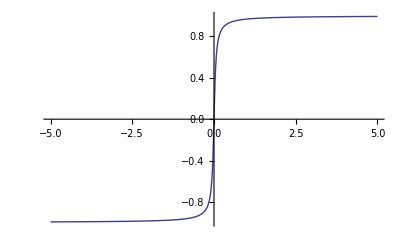

```mathematica
lambda = 20;
Plot[2/π*ArcTan[lambda*x], {x,-5,5}]
```